```mathematica
Quit[];
```

```mathematica
$LoadAddOns = {"FeynArts","FeynHelpers"};
<< FeynCalc`
$FAVerbose = 0;
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->FileNameJoin[{NotebookDirectory[],"Massless_3scalar_FA"}]]
```

Successfully patched FeynArts.

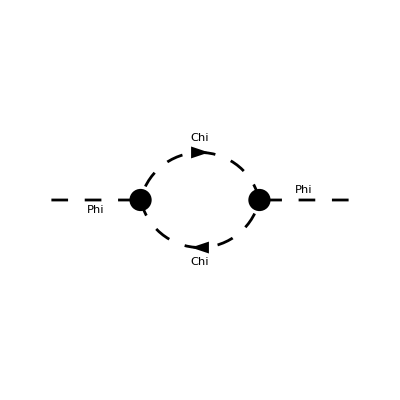

```mathematica
OneLoopDiags = InsertFields[CreateTopologies[1, 1 -> 1, ExcludeTopologies->{Tadpoles,WFCorrections}],S[1]->S[1], InsertionLevel->{Classes},Model -> FileNameJoin[{NotebookDirectory[],"Massless_3scalar_FA", "Massless_3scalar_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Massless_3scalar_FA", "Massless_3scalar_FA"}]];
Paint[OneLoopDiags, Numbering->None, SheetHeader->None,ColumnsXRows->{1,1},ImageSize->{100,100}];
```

```mathematica
OneLoopAmp[0]=FCFAConvert[CreateFeynAmp[OneLoopDiags,PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->D,List->False,FinalSubstitutions->{mPhi->m,mChi->0}]
```

c3^2/(q^2.(q-p)^2)

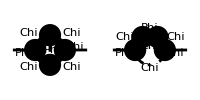

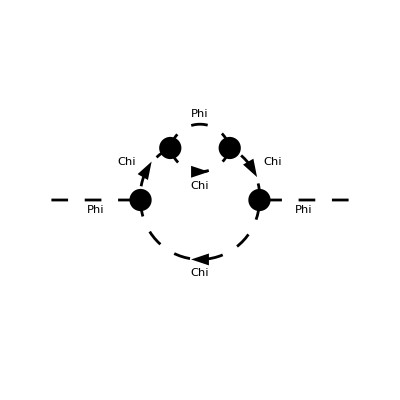

```mathematica
TwoLoopDiags = InsertFields[CreateTopologies[2, 1 -> 1, ExcludeTopologies->{Tadpoles,WFCorrections}],S[1]->S[1], InsertionLevel->{Classes},Model -> FileNameJoin[{NotebookDirectory[],"Massless_3scalar_FA", "Massless_3scalar_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Massless_3scalar_FA", "Massless_3scalar_FA"}]];
Paint[TwoLoopDiags, Numbering->None, SheetHeader->None,ColumnsXRows->{2,1},ImageSize->{200,100}];
```

```mathematica
TwoLoopAmp[0]=FCFAConvert[CreateFeynAmp[TwoLoopDiags,PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q,r},ChangeDimension->D,List->True,DropSumOver->True,FinalSubstitutions->{mPhi->m,mChi->0}]
```

{(ⅈ c3^4)/(q^2.r^2.((q+r)^2-m^2).(r-p)^2.(p+q)^2),(ⅈ c3^4)/(q^2.(r^2-m^2).((q-p)^2)^2.(p-q+r)^2),(ⅈ c3^4)/(q^2.(r^2-m^2).((q-p)^2)^2.(p-q+r)^2)}

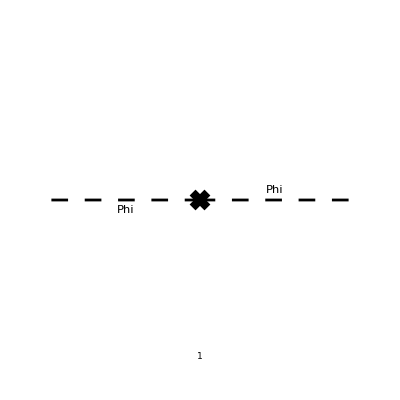

```mathematica
OneLoopCTDiags = InsertFields[CreateCTTopologies[1, 1 -> 1,ExcludeTopologies->{Tadpoles,WFCorrectionCTs}],S[1]->S[1], InsertionLevel->{Classes}, Model -> FileNameJoin[{NotebookDirectory[],"Massless_3scalar_FA", "Massless_3scalar_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Massless_3scalar_FA", "Massless_3scalar_FA"}]];
Paint[OneLoopCTDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{2,1},ImageSize->{200,100}];
```

```mathematica
OneLoopCTAmp[0]=FCFAConvert[CreateFeynAmp[OneLoopCTDiags,PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},ChangeDimension->D,List->False,FinalSubstitutions->{mPhi->m,mChi->0}]
```

ⅈ p^2 FR$deltaZ({Phi,Phi},{{}})-ⅈ m (2 FR$delta({m},{})+m FR$deltaZ({Phi,Phi},{{}}))

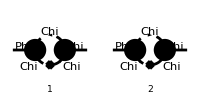

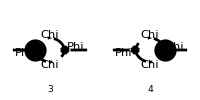

```mathematica
TwoLoopCTDiags = InsertFields[CreateCTTopologies[2, 1 -> 1,ExcludeTopologies->{Tadpoles,WFCorrectionCTs}],S[1]->S[1], InsertionLevel->{Classes}, Model -> FileNameJoin[{NotebookDirectory[],"Massless_3scalar_FA", "Massless_3scalar_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Massless_3scalar_FA", "Massless_3scalar_FA"}]];
Paint[TwoLoopCTDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{2,1},ImageSize->{200,100}];
```

```mathematica
TwoLoopCTAmp[0]=FCFAConvert[CreateFeynAmp[TwoLoopCTDiags,PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->D,List->False,FinalSubstitutions->{mPhi->m,mChi->0}]
```

(c3 (2 c3 FR$deltaZ({Chi,Chi},{{}})+2 FR$delta({c3},{})+c3 FR$deltaZ({Phi,Phi},{{}})))/(q^2.(q-p)^2)-(2 c3^2 q^2 FR$deltaZ({Chi,Chi},{{}}))/((q^2)^2.(p+q)^2)

```mathematica
FCClearScalarProducts[];
ScalarProduct[p,p]=s;
```

```mathematica
OneLoopAmp[1]=OneLoopAmp[0]//TID[#,q,ToPaVe->True]&//ChangeDimension[PaXEvaluate[#],4]&;
TwoLoopCTAmp[1]=TwoLoopCTAmp[0]//TID[#,q,ToPaVe->True]&//ChangeDimension[PaXEvaluate[#],4]&;
```

Get::noopen: Cannot open C:\Users\hypercube256\AppData\Roaming\Mathematica\Applications\X\PacletInfo.m.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[2,FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3}].

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

ToExpression::notstrbox: FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3} is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

Get::noopen: Cannot open C:\Users\hypercube256\AppData\Roaming\Mathematica\Applications\X\PacletInfo.m.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[2,FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3}].

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

ToExpression::notstrbox: FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3} is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

```mathematica
OneLoopAmp[1]
OneLoopCTAmp[0]
TwoLoopCTAmp[1]
```

(ⅈ π^2 c3^2)/ε-ⅈ π^2 c3^2 (-log(-μ^2/(π s))+ℽ-2)

ⅈ s FR$deltaZ({Phi,Phi},{{}})-ⅈ m (2 FR$delta({m},{})+m FR$deltaZ({Phi,Phi},{{}}))

(ⅈ π^2 c3 (2 FR$delta({c3},{})+c3 FR$deltaZ({Phi,Phi},{{}})))/ε-ⅈ π^2 c3 (-log(-μ^2/(π s))+ℽ-2) (2 FR$delta({c3},{})+c3 FR$deltaZ({Phi,Phi},{{}}))

```mathematica
TwoLoopAmp[1]=FCFeynmanParametrize[#,{q,r},Names->x,FCReplaceD->{D->4-2Epsilon},FeynmanIntegralPrefactor->"Textbook"]&/@TwoLoopAmp[0]
```

((x(1) x(3)+x(2) x(3)+x(5) x(3)+x(1) x(4)+x(2) x(4)+x(1) x(5)+x(2) x(5)+x(4) x(5))^(3 ε-1) (m^2 x(1) (x(5))^2+m^2 x(2) (x(5))^2+m^2 x(3) (x(5))^2+m^2 x(4) (x(5))^2+m^2 x(1) x(3) x(5)+m^2 x(2) x(3) x(5)+m^2 x(1) x(4) x(5)+m^2 x(2) x(4) x(5)-s x(1) x(2) x(3)-s x(1) x(2) x(4)-s x(1) x(3) x(4)-s x(2) x(3) x(4)-s x(1) x(2) x(5)-s x(2) x(3) x(5)-s x(1) x(4) x(5)-s x(3) x(4) x(5))^(-2 ε-1) | ⅈ c3^4 2^(4 ε-8) π^(2 ε-4) 2 ε+1 | {x(1),x(2),x(3),x(4),x(5)}
x(2) (x(1) x(3)+x(2) x(3)+x(4) x(3)+x(1) x(4)+x(2) x(4))^(3 ε-1) (m^2 x(1) (x(3))^2+m^2 x(2) (x(3))^2+m^2 (x(3))^2 x(4)+m^2 x(1) x(3) x(4)+m^2 x(2) x(3) x(4)-s x(1) x(2) x(3)-s x(1) x(2) x(4)-s x(1) x(3) x(4))^(-2 ε-1) | ⅈ c3^4 2^(4 ε-8) π^(2 ε-4) 2 ε+1 | {x(1),x(2),x(3),x(4)}
x(2) (x(1) x(3)+x(2) x(3)+x(4) x(3)+x(1) x(4)+x(2) x(4))^(3 ε-1) (m^2 x(1) (x(3))^2+m^2 x(2) (x(3))^2+m^2 (x(3))^2 x(4)+m^2 x(1) x(3) x(4)+m^2 x(2) x(3) x(4)-s x(1) x(2) x(3)-s x(1) x(2) x(4)-s x(1) x(3) x(4))^(-2 ε-1) | ⅈ c3^4 2^(4 ε-8) π^(2 ε-4) 2 ε+1 | {x(1),x(2),x(3),x(4)})

```mathematica
TwoLoopAmp[1][[1]][[1]]
TwoLoopAmp[1][[2]][[1]]
TwoLoopAmp[1][[3]][[1]]
```

(x(1) x(3)+x(2) x(3)+x(5) x(3)+x(1) x(4)+x(2) x(4)+x(1) x(5)+x(2) x(5)+x(4) x(5))^(3 ε-1) (m^2 x(1) (x(5))^2+m^2 x(2) (x(5))^2+m^2 x(3) (x(5))^2+m^2 x(4) (x(5))^2+m^2 x(1) x(3) x(5)+m^2 x(2) x(3) x(5)+m^2 x(1) x(4) x(5)+m^2 x(2) x(4) x(5)-s x(1) x(2) x(3)-s x(1) x(2) x(4)-s x(1) x(3) x(4)-s x(2) x(3) x(4)-s x(1) x(2) x(5)-s x(2) x(3) x(5)-s x(1) x(4) x(5)-s x(3) x(4) x(5))^(-2 ε-1)

x(2) (x(1) x(3)+x(2) x(3)+x(4) x(3)+x(1) x(4)+x(2) x(4))^(3 ε-1) (m^2 x(1) (x(3))^2+m^2 x(2) (x(3))^2+m^2 (x(3))^2 x(4)+m^2 x(1) x(3) x(4)+m^2 x(2) x(3) x(4)-s x(1) x(2) x(3)-s x(1) x(2) x(4)-s x(1) x(3) x(4))^(-2 ε-1)

x(2) (x(1) x(3)+x(2) x(3)+x(4) x(3)+x(1) x(4)+x(2) x(4))^(3 ε-1) (m^2 x(1) (x(3))^2+m^2 x(2) (x(3))^2+m^2 (x(3))^2 x(4)+m^2 x(1) x(3) x(4)+m^2 x(2) x(3) x(4)-s x(1) x(2) x(3)-s x(1) x(2) x(4)-s x(1) x(3) x(4))^(-2 ε-1)

```mathematica
TwoLoopAmp[0]
```

{(ⅈ c3^4)/(q^2.r^2.((q+r)^2-m^2).(r-p)^2.(p+q)^2),(ⅈ c3^4)/(q^2.(r^2-m^2).((q-p)^2)^2.(p-q+r)^2),(ⅈ c3^4)/(q^2.(r^2-m^2).((q-p)^2)^2.(p-q+r)^2)}

```mathematica
{amp,topos}=FCLoopFindTopologies[TwoLoopAmp[0],{q,r}];
subtopos=FCLoopFindSubtopologies[topos];
mappings=FCLoopFindTopologyMappings[topos,PreferredTopologies->subtopos];
ampFinal=FCLoopApplyTopologyMappings[amp,mappings];
```

FCLoopFindTopologies: Number of the initial candidate topologies: 2

FCLoopFindTopologies: Number of the identified unique topologies: 2

FCLoopFindTopologies: Number of the preferred topologies among the unique topologies: 0

FCLoopFindTopologies: Number of the identified subtopologies: 0

FCLoopFindTopologyMappings: Found 1 mapping relations

FCLoopFindTopologyMappings: Final number of independent topologies: 1

```mathematica
ampFinal
```

{ⅈ c3^4 G^fctopology1(1,1,1,1,1),ⅈ c3^4 G^fctopology1(0,1,2,1,1),ⅈ c3^4 G^fctopology1(0,1,2,1,1)}

```mathematica
resPreFinal=Collect2[Total[ampFinal],GLI];
```

2 ⅈ c3^4 G^fctopology1(0,1,2,1,1)+ⅈ c3^4 G^fctopology1(1,1,1,1,1)

```mathematica
integralMappings=FCLoopFindIntegralMappings[Cases2[resPreFinal,GLI],mappings[[2]]]
```

{{},{G^fctopology1(0,1,2,1,1),G^fctopology1(1,1,1,1,1)}}

```mathematica
resFinal=Collect2[resPreFinal/. integralMappings[[1]],GLI]
```

2 ⅈ c3^4 G^fctopology1(0,1,2,1,1)+ⅈ c3^4 G^fctopology1(1,1,1,1,1)

```mathematica
aux1=FCFeynmanParametrize[integralMappings[[2]][[1]],mappings[[2]],Names->x,FCReplaceD->{D->4-2Epsilon}]
preInt1=Integrate[aux1[[1]]/.x[1]->1,{x[2],0,Infinity},Assumptions->{ep>0,x[3]>=0,pp>0,ep<1}]
preInt2=Integrate[preInt1,{x[3],0,Infinity},Assumptions->{ep>0,pp>0,ep<1}]
int2L=SelectNotFree[preInt2,pp](Series[E^(2ep*EulerGamma)SelectFree[preInt2,pp]aux1[[2]],{ep,0,2}]//Normal//SimplifyPolyLog)
```

{x(2) (x(1) x(3)+x(2) x(3)+x(4) x(3)+x(1) x(4)+x(2) x(4))^(3 ε-1) (m^2 x(1) (x(4))^2+m^2 x(2) (x(4))^2+m^2 x(3) (x(4))^2+m^2 x(1) x(3) x(4)+m^2 x(2) x(3) x(4)-s x(1) x(2) x(3)-s x(1) x(2) x(4)-s x(1) x(3) x(4))^(-2 ε-1),-2 ε+1,{x(1),x(2),x(3),x(4)}}

Infinity::indet: Indeterminate expression -∞+∞ encountered.

Integrate[x(2) (x(2) x(3)+x(4) x(3)+x(3)+x(2) x(4)+x(4))^(3 ε-1) (m^2 x(2) (x(4))^2+m^2 x(3) (x(4))^2+m^2 (x(4))^2+m^2 x(2) x(3) x(4)+m^2 x(3) x(4)-s x(2) x(3)-s x(2) x(4)-s x(3) x(4))^(-2 ε-1),{x(2),0,∞},Assumptions→{ep>0,x(3)≥0,pp>0,ep<1}]

$Aborted

-2 ℽ^2 ep^2 preInt2 2 ε+1-2 ℽ ep preInt2 2 ε+1-preInt2 2 ε+1

```mathematica
aux1=FCFeynmanParametrize[SFAD[q1,q1+p],{q1},Names->x,FCReplaceD->{D->4-2ep}]
preInt1=Integrate[aux1[[1]]/.x[1]->1-x[2],{x[2],0,1},Assumptions->{ep>0,pp>0,ep<1}]
int1L=SelectNotFree[preInt1,pp](Series[E^(ep*EulerGamma)SelectFree[preInt1,pp]aux1[[2]],{ep,0,2}]//Normal//SimplifyPolyLog)
```

```mathematica
ruleMasters=Thread[Rule[integralMappings[[2]],{int2L,int1L^2}]]
```